## Global HAR

```mathematica
ntFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*_countRYPWall.dat"]
tlFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*_countRYPWall.dat"]
taFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*_countRYPWall.dat"]
```

{/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_NT01har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_NT02har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_NT03har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_NT04har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_NT05har_countRYPWall.dat}

{/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL01har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL02har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL03har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL04har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TL05har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TL12har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TL13har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TL14har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TL01harb_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TL03hara_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TL04harb_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TL05harb_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL02harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL03harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL04harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL05harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL06harc_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/110318/Analysis/MAX_TL07harc_countRYPWall.dat}

{/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA01har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA02har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA03har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA04har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA06har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA07har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA08har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/091018/Analysis/MAX_TA09har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA11har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA12har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA13har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA14har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA16har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA17har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA18har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/092618/Analysis/MAX_TA20har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TA04_har_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TA06_har_2cells_countRYPWall.dat,/Users/ccialek/Desktop/HAR cells/102418/Analysis/MAX_TA06_har_bottom_countRYPWall.dat}

### Spot counts

```mathematica
ntCounts= Table[<<(ntFiles[[i]]),{i,1,Length@ntFiles,1}];
tlCounts= Table[<<(tlFiles[[i]]),{i,1,Length@tlFiles,1}];
taCounts= Table[<<(taFiles[[i]]),{i,1,Length@taFiles,1}];
```

```mathematica
ntCountsTot=Total[ Table[ntCounts[[i]],{i,1,Length@ntCounts}]];
tlCountsTot=Total[ Table[tlCounts[[i]],{i,1,Length@tlCounts}]];
taCountsTot=Total[ Table[taCounts[[i]],{i,1,Length@taCounts}]];
Dimensions/@ntCountsTot
Dimensions/@tlCountsTot
Dimensions/@taCountsTot
```

{{5,2},{5,65,2}}

{{5,2},{5,65,2}}

{{5,2},{5,65,2}}

```mathematica
myTimes = ntCounts[[1,2,1,All,1]]
Length@myTimes
Length@ntCountsTot[[2,1,All,2]]
```

{-4,-3,-2,-1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60}

65

65

```mathematica
ntCountsTot[[1]]
```

{{5 mytimes,5 countRedOnly},{5 mytimes,5 countYellowOnly},{5 mytimes,5 countPurpleOnly},{5 mytimes,5 countWhiteOnly},{5 mytimes,5 total spot count}}

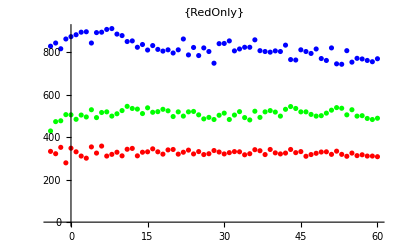

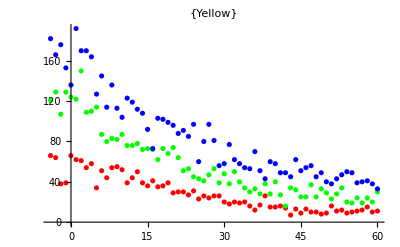

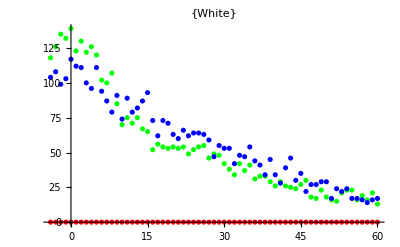

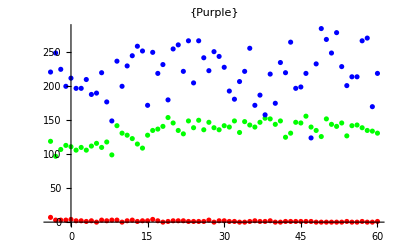

```mathematica
pRedNtTlTa=ListPlot[{Transpose[{myTimes,ntCountsTot[[2,1,All,2]]}],Transpose[{myTimes,tlCountsTot[[2,1,All,2]]}],Transpose[{myTimes,taCountsTot[[2,1,All,2]]}]},PlotStyle->{Red,Green,Blue},PlotLabel->{"RedOnly"}]
pRedNtTlTa=ListPlot[{Transpose[{myTimes,ntCountsTot[[2,2,All,2]]}],Transpose[{myTimes,tlCountsTot[[2,2,All,2]]}],Transpose[{myTimes,taCountsTot[[2,2,All,2]]}]},PlotStyle->{Red,Green,Blue},PlotLabel->{"Yellow"}]
pRedNtTlTa=ListPlot[{Transpose[{myTimes,ntCountsTot[[2,4,All,2]]}],Transpose[{myTimes,tlCountsTot[[2,4,All,2]]}],Transpose[{myTimes,taCountsTot[[2,4,All,2]]}]},PlotStyle->{Red,Green,Blue},PlotLabel->{"White"}]
pRedNtTlTa=ListPlot[{Transpose[{myTimes,ntCountsTot[[2,3,All,2]]}],Transpose[{myTimes,tlCountsTot[[2,3,All,2]]}],Transpose[{myTimes,taCountsTot[[2,3,All,2]]}]},PlotStyle->{Red,Green,Blue},PlotLabel->{"Purple"}]
```

## Intensities from gaussian fits HAR

### Import:

```mathematica
ntYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*YELLOW__myRGaussInts.m"];
tlYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*YELLOW__myRGaussInts.m"];
taYFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*YELLOW__myRGaussInts.m"];
```

```mathematica
ntWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*WHITE__myRGaussInts.m"];
tlWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*WHITE__myRGaussInts.m"];
taWFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*WHITE__myRGaussInts.m"];
```

```mathematica
ntPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_NT*PURPLE__myRGaussInts.m"];
tlPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TL*PURPLE__myRGaussInts.m"];
taPFiles = FileNames["/Users/ccialek/Desktop/HAR cells/*/Analysis/MAX_TA*PURPLE__myRGaussInts.m"];
```

```mathematica
Length@ntYFiles
Length@tlYFiles
Length@taYFiles
movieLength = Length@taYInts0[[1,2]]
```

5

18

19

65

```mathematica
ntYInts= Table[<<(ntYFiles[[i]]),{i,1,Length@ntYFiles,1}];
tlYInts= Table[<<(tlYFiles[[i]]),{i,1,Length@tlYFiles,1}];
taYInts= Table[<<(taYFiles[[i]]),{i,1,Length@taYFiles,1}];
ntWInts= Table[<<(ntWFiles[[i]]),{i,1,Length@ntWFiles,1}];
tlWInts= Table[<<(tlWFiles[[i]]),{i,1,Length@tlWFiles,1}];
taWInts= Table[<<(taWFiles[[i]]),{i,1,Length@taWFiles,1}];
ntPInts= Table[<<(ntPFiles[[i]]),{i,1,Length@ntPFiles,1}];
tlPInts= Table[<<(tlPFiles[[i]]),{i,1,Length@tlPFiles,1}];
taPInts= Table[<<(taPFiles[[i]]),{i,1,Length@taPFiles,1}];
```

```mathematica
(*ntYInts= Table[Table[Select[Flatten[ntYInts0[[All,channel,frame]],1],#<5&],{channel,2,4,1}],{frame,1,movieLength,1}];
tlYInts= Table[Select[Flatten[tlYInts0[[All,3,frame]],1],#<5&],{frame,1,movieLength,1}];
taYInts= Table[Select[Flatten[taYInts0[[All,3,frame]],1],#<5&],{frame,1,movieLength,1}];
ntWInts= Table[Select[Flatten[ntWInts0[[All,3,frame]],1],#<5&],{frame,1,movieLength,1}];
tlWInts= Table[Select[Flatten[tlWInts0[[All,3,frame]],1],#<5&],{frame,1,movieLength,1}];
taWInts=Table[Select[Flatten[taWInts0[[All,3,frame]],1],#<5&],{frame,1,movieLength,1}];
ntPInts= Table[Select[Flatten[ntPInts0[[All,3,frame]],1],#<5&],{frame,1,movieLength,1}];
tlPInts= Table[Select[Flatten[tlPInts0[[All,3,frame]],1],#<5&],{frame,1,movieLength,1}];
taPInts= Table[Select[Flatten[taWInts0[[All,3,frame]],1],#<5&],{frame,1,movieLength,1}];
```

### FUTURE: DEV THIS INTO A FILTER STEP!! Visualize to filter (ONLY filtering nonzeros up to this point...)

```mathematica
ListPlot[{Flatten@ntInts[[1,2]],Flatten@ntInts[[2,2]],Flatten@ntInts[[3,2]],Flatten@ntInts[[4,2]],Flatten@ntInts[[5,2]]},PlotStyle->Red,PlotRange->All]
ListPlot[{Flatten@ntInts[[1,3]],Flatten@ntInts[[2,3]],Flatten@ntInts[[3,3]],Flatten@ntInts[[4,3]],Flatten@ntInts[[5,3]]},PlotStyle->Green,PlotRange->All]
ListPlot[{Flatten@ntInts[[1,4]],Flatten@ntInts[[2,4]],Flatten@ntInts[[3,4]],Flatten@ntInts[[4,4]],Flatten@ntInts[[5,4]]},PlotStyle->Blue,PlotRange->All]
```

Part::partd: Part specification ntInts⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification ntInts⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification ntInts⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
redmean = Mean@Flatten@{ntInts[[1,2]],ntInts[[2,2]],ntInts[[3,2]],ntInts[[4,2]],ntInts[[5,2]]}
stdev2 = 2*StandardDeviation@Flatten@{ntInts[[1,2]],ntInts[[2,2]],ntInts[[3,2]],ntInts[[4,2]],ntInts[[5,2]]}
```

Part::partd: Part specification ntInts⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/5 (ntInts⟦1,2⟧+ntInts⟦2,2⟧+ntInts⟦3,2⟧+ntInts⟦4,2⟧+ntInts⟦5,2⟧)

Part::partd: Part specification ntInts⟦1,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/(√5)(√(Conjugate[ntInts⟦1,2⟧] (4 ntInts⟦1,2⟧-ntInts⟦2,2⟧-ntInts⟦3,2⟧-ntInts⟦4,2⟧-ntInts⟦5,2⟧)+Conjugate[ntInts⟦2,2⟧] (-ntInts⟦1,2⟧+4 ntInts⟦2,2⟧-ntInts⟦3,2⟧-ntInts⟦4,2⟧-ntInts⟦5,2⟧)+Conjugate[ntInts⟦3,2⟧] (-ntInts⟦1,2⟧-ntInts⟦2,2⟧+4 ntInts⟦3,2⟧-ntInts⟦4,2⟧-ntInts⟦5,2⟧)+Conjugate[ntInts⟦4,2⟧] (-ntInts⟦1,2⟧-ntInts⟦2,2⟧-ntInts⟦3,2⟧+4 ntInts⟦4,2⟧-ntInts⟦5,2⟧)+Conjugate[ntInts⟦5,2⟧] (-ntInts⟦1,2⟧-ntInts⟦2,2⟧-ntInts⟦3,2⟧-ntInts⟦4,2⟧+4 ntInts⟦5,2⟧)))

```mathematica
greenmean = Mean@Flatten@{ntInts[[1,3]],ntInts[[2,3]],ntInts[[3,3]],ntInts[[4,3]],ntInts[[5,3]]}
stdev2 = 2*StandardDeviation@Flatten@{ntInts[[1,3]],ntInts[[2,3]],ntInts[[3,3]],ntInts[[4,3]],ntInts[[5,3]]}
```

Part::partd: Part specification ntInts⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/5 (ntInts⟦1,3⟧+ntInts⟦2,3⟧+ntInts⟦3,3⟧+ntInts⟦4,3⟧+ntInts⟦5,3⟧)

Part::partd: Part specification ntInts⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/(√5)(√(Conjugate[ntInts⟦1,3⟧] (4 ntInts⟦1,3⟧-ntInts⟦2,3⟧-ntInts⟦3,3⟧-ntInts⟦4,3⟧-ntInts⟦5,3⟧)+Conjugate[ntInts⟦2,3⟧] (-ntInts⟦1,3⟧+4 ntInts⟦2,3⟧-ntInts⟦3,3⟧-ntInts⟦4,3⟧-ntInts⟦5,3⟧)+Conjugate[ntInts⟦3,3⟧] (-ntInts⟦1,3⟧-ntInts⟦2,3⟧+4 ntInts⟦3,3⟧-ntInts⟦4,3⟧-ntInts⟦5,3⟧)+Conjugate[ntInts⟦4,3⟧] (-ntInts⟦1,3⟧-ntInts⟦2,3⟧-ntInts⟦3,3⟧+4 ntInts⟦4,3⟧-ntInts⟦5,3⟧)+Conjugate[ntInts⟦5,3⟧] (-ntInts⟦1,3⟧-ntInts⟦2,3⟧-ntInts⟦3,3⟧-ntInts⟦4,3⟧+4 ntInts⟦5,3⟧)))

```mathematica
bluemean = Mean@Flatten@{ntInts[[1,4]],ntInts[[2,4]],ntInts[[3,4]],ntInts[[4,4]],ntInts[[5,4]]}
stdev2 = 2*StandardDeviation@Flatten@{ntInts[[1,4]],ntInts[[2,4]],ntInts[[3,4]],ntInts[[4,4]],ntInts[[5,4]]}
```

Part::partd: Part specification ntInts⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/5 (ntInts⟦1,4⟧+ntInts⟦2,4⟧+ntInts⟦3,4⟧+ntInts⟦4,4⟧+ntInts⟦5,4⟧)

Part::partd: Part specification ntInts⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

1/(√5)(√(Conjugate[ntInts⟦1,4⟧] (4 ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦2,4⟧] (-ntInts⟦1,4⟧+4 ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦3,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧+4 ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦4,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧+4 ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦5,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧+4 ntInts⟦5,4⟧)))

```mathematica
mean+stdev2
mean-stdev2
```

mean+1/(√5)(√(Conjugate[ntInts⟦1,4⟧] (4 ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦2,4⟧] (-ntInts⟦1,4⟧+4 ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦3,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧+4 ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦4,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧+4 ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦5,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧+4 ntInts⟦5,4⟧)))

mean-1/(√5)(√(Conjugate[ntInts⟦1,4⟧] (4 ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦2,4⟧] (-ntInts⟦1,4⟧+4 ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦3,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧+4 ntInts⟦3,4⟧-ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦4,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧+4 ntInts⟦4,4⟧-ntInts⟦5,4⟧)+Conjugate[ntInts⟦5,4⟧] (-ntInts⟦1,4⟧-ntInts⟦2,4⟧-ntInts⟦3,4⟧-ntInts⟦4,4⟧+4 ntInts⟦5,4⟧)))

```mathematica
Histogram[Flatten@{ntInts[[1,3]],ntInts[[2,3]],ntInts[[3,3]],ntInts[[4,3]],ntInts[[5,3]]}, ChartStyle->Green]
Histogram[Flatten@{ntInts[[1,4]],ntInts[[2,4]],ntInts[[3,4]],ntInts[[4,4]],ntInts[[5,4]]},100000, ChartStyle->Blue]
```

Part::partd: Part specification ntInts⟦1,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,3⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification ntInts⟦1,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦2,4⟧ is longer than depth of object.

Part::partd: Part specification ntInts⟦3,4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

### Total and count intensities

need to filter out shithead intensts out of blue

```mathematica
(*ntYInts=Table[Table[Select[ntYInts0[[All,channel,frame]],#<5&],{channel,2,4,1}],{frame,1,movieLength,1}];
```

```mathematica
Dimensions@ntYInts
Dimensions/@ntYInts0[[1]]
ntYInts
```

{65,3,0}

{{3,1},{65},{65},{65}}

{{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}},{{},{},{}}}

{{3,1},{65},{65},{65}}

{65}

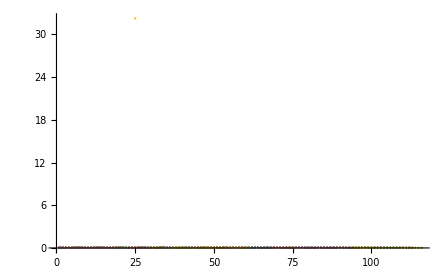

```mathematica
Dimensions/@tlWInts[[1]]
Dimensions@ Table[Flatten[tlWInts[[All,3,frame]],1],{frame,1,65,1}]
 Table[Flatten[taWInts[[All,3,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->All]&
```

```mathematica
Select[{1,2,4,7,6,2},#>2&]
```

{4,7,6}

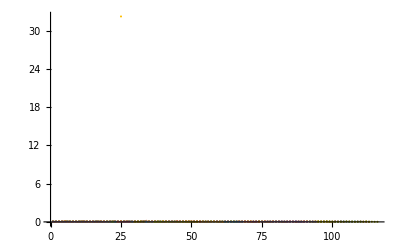
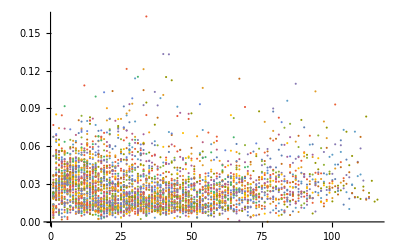

```mathematica
Row[{ Table[Flatten[taWInts[[All,3,frame]],1],{frame,1,65,1}]//ListPlot[#,PlotRange->All, ImageSize->400]&,
Table[Select[Flatten[taWInts[[All,3,frame]],1],#<2&],{frame,1,65,1}]//ListPlot[#,PlotRange->All,ImageSize->400]&  }]
(*This is showing that without filtering I'm getting some crazy intensities.... *)
```

```mathematica
ntYIntsTotRGB= Table[Table[Total@(Total/@ntYInts[[All,j,i]]),{i,1,Length@ntYInts[[1,2]],1}],{j,2,Length@ntYInts[[2]],1}];
tlYIntsTotRGB= Table[Table[Total@(Total/@tlYInts[[All,j,i]]),{i,1,Length@tlYInts[[1,2]],1}],{j,2,Length@tlYInts[[2]],1}];
taYIntsTotRGB= Table[Table[Total@(Total/@taYInts[[All,j,i]]),{i,1,Length@taYInts[[1,2]],1}],{j,2,Length@taYInts[[2]],1}];
```

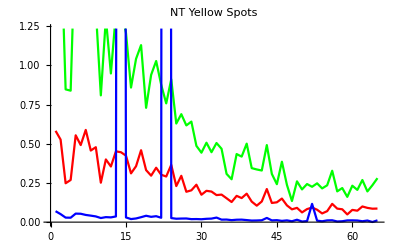

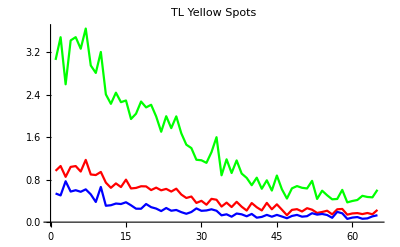

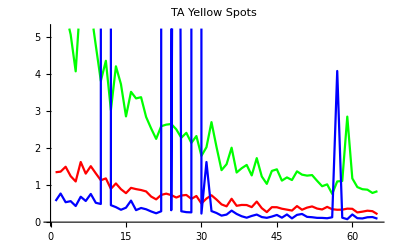

```mathematica
ListLinePlot[ntYIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT Yellow Spots"]
ListLinePlot[tlYIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotRange->All,PlotLabel->"TL Yellow Spots"]
ListLinePlot[taYIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA Yellow Spots"]
```

```mathematica
ntWIntsTotRGB= Table[Table[Total@(Total/@ntWInts[[All,j,i]]),{i,1,Length@ntWInts[[1,2]],1}],{j,2,Length@ntWInts[[2]],1}];
tlWIntsTotRGB= Table[Table[Total@(Total/@tlWInts[[All,j,i]]),{i,1,Length@tlWInts[[1,2]],1}],{j,2,Length@tlWInts[[2]],1}];
taWIntsTotRGB= Table[Table[Total@(Total/@taWInts[[All,j,i]]),{i,1,Length@taWInts[[1,2]],1}],{j,2,Length@taWInts[[2]],1}];
```

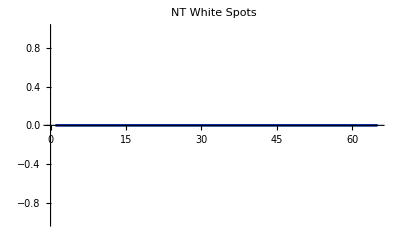

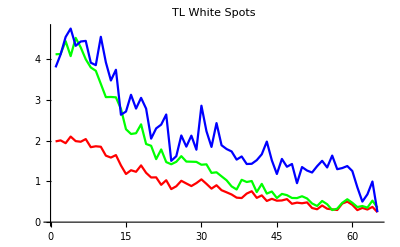

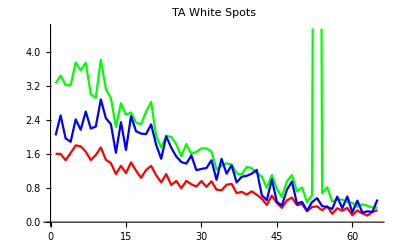

```mathematica
ListLinePlot[ntWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT White Spots"]
ListLinePlot[tlWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TL White Spots",PlotRange->All]
ListLinePlot[taWIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA White Spots"]
```

### Find and subtract out the immobile fraction, and normalize to start at 1 Replot Total and count intensities

## Yellow spots

#### Input:

```mathematica
myTimes = ntCounts[[1,2,1,All,1]]*60;
Length@myTimes
Length@ntCountsTot[[2,1,All,2]]
```

65

65

```mathematica
(*green intensity *) ntGIntsY0 = Table[Total@(Total/@ntYInts[[All,3,i]] ),{i,1,Length@ntYInts[[1,2]],1}];
(*green intensity *) tlGIntsY0 = Table[Total@(Total/@tlYInts[[All,3,i]]),{i,1,Length@tlYInts[[1,2]],1}];
(*green intensity *) taGIntsY0 = Table[Total@(Total/@taYInts[[All,3,i]]),{i,1,Length@taYInts[[1,2]],1}];
```

#### FIRST, find the Immobile Fraction and subtract that out of the Y value...

#### NT: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = ntGIntsY0
```

{1.68714,1.87299,0.846853,0.838484,1.90108,1.61927,1.70552,1.34644,1.35595,0.80855,1.29976,0.94822,1.33406,1.34752,1.20734,0.858353,1.04138,1.12906,0.729174,0.939275,1.02768,0.876224,0.757451,0.91118,0.628934,0.68866,0.616897,0.641245,0.486622,0.442937,0.506565,0.446126,0.504671,0.468002,0.307664,0.273466,0.434165,0.417955,0.500584,0.344476,0.33594,0.32927,0.491355,0.307508,0.242012,0.385429,0.2376,0.134793,0.260131,0.208787,0.242898,0.225503,0.247504,0.215137,0.23491,0.327707,0.196272,0.217429,0.161184,0.232284,0.205593,0.268716,0.195937,0.235678,0.280559}

```mathematica
Mean[mySpots[[40;;All]]]
immobileFraction = Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

0.260178

0.236003

0.231006

0.232388

```mathematica
ntGIntsY00 = mySpots-immobileFraction ;
```

#### TL: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = tlGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
immobileFraction = Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

0.581445

0.550949

0.519346

0.474404

```mathematica
tlGIntsY00 = mySpots-immobileFraction ;
```

#### TA: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = taGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
immobileFraction = Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

1.20049

1.1696

1.14294

1.12565

```mathematica
taGIntsY00 = mySpots-immobileFraction ;
```

#### Normalizing Intensity...

```mathematica
(*normalized green intensity *) ntGIntsY = ntGIntsY00 /Mean[ntGIntsY00[[1;;7]]];
(*normalized green intensity *) tlGIntsY = tlGIntsY00 /Mean[tlGIntsY00[[1;;7]]];
(*normalized green intensity *)   taGIntsY =  taGIntsY00/Mean[taGIntsY00[[1;;7]]];
```

```mathematica
(*normalized green intensity *) ntGIntsYTime = Transpose[{myTimes,ntGIntsY}] 
(*normalized green intensity *) tlGIntsYTime =  Transpose[{myTimes,tlGIntsY}];
(*normalized green intensity *)   taGIntsYTime =   Transpose[{myTimes,taGIntsY}];
```

{{-240,1.15179},{-180,1.2993},{-120,0.48484},{-60,0.478197},{0,1.32159},{60,1.09792},{120,1.16638},{180,0.881367},{240,0.888914},{300,0.454438},{360,0.844319},{420,0.565296},{480,0.871545},{540,0.882224},{600,0.770964},{660,0.493967},{720,0.639238},{780,0.708833},{840,0.391436},{900,0.558195},{960,0.628366},{1020,0.508151},{1080,0.41388},{1140,0.535897},{1200,0.311875},{1260,0.359279},{1320,0.30232},{1380,0.321645},{1440,0.198919},{1500,0.164246},{1560,0.214749},{1620,0.166777},{1680,0.213245},{1740,0.18414},{1800,0.0568781},{1860,0.0297348},{1920,0.157284},{1980,0.144417},{2040,0.210001},{2100,0.0860963},{2160,0.0793213},{2220,0.0740272},{2280,0.202676},{2340,0.0567539},{2400,0.00476932},{2460,0.118602},{2520,0.00126768},{2580,-0.0803316},{2640,0.0191506},{2700,-0.0216017},{2760,0.00547239},{2820,-0.00833385},{2880,0.00912868},{2940,-0.0165615},{3000,-0.000867292},{3060,0.0727868},{3120,-0.0315349},{3180,-0.0147429},{3240,-0.0593848},{3300,-0.00295176},{3360,-0.0241372},{3420,0.0259647},{3480,-0.0318007},{3540,-0.000257891},{3600,0.0353645}}

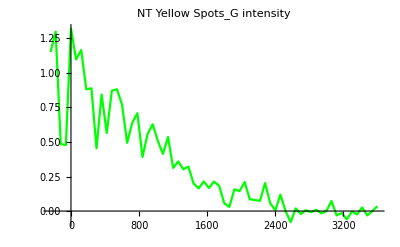

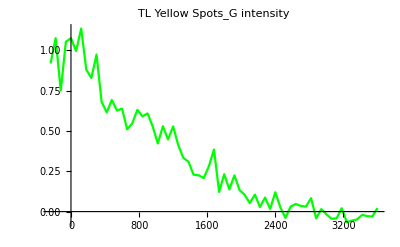

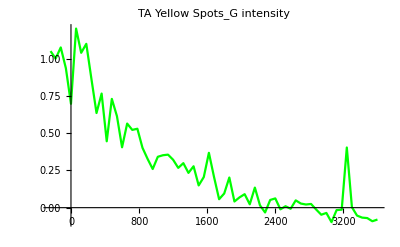

```mathematica
pNT = ListLinePlot[ntGIntsYTime,PlotStyle->{Green},PlotLabel->"NT Yellow Spots_G intensity"]
pTL = ListLinePlot[tlGIntsYTime,PlotStyle->{Green},PlotLabel->"TL Yellow Spots_G intensity"]
pTA = ListLinePlot[taGIntsYTime,PlotStyle->{Green},PlotLabel->"TA Yellow Spots_G intensity"]
```

#### Define tag and protein lengths in AAs

```mathematica
l2 = (1010/3)//N   (*Length of smFLAG tag in AAs*)
l1 = (4645/3)//N   (*Length of KDM5B in AAs*)
```

336.667

1548.33

```mathematica
fraction = (l1/(l1+l2/2))   (*Once the fluorescence drops by this much, this is t0*)
```

0.901942

#### Select the data that falls within the linear range: l1/(l1+l2/2) --> linear part MANUAL INPUT: Set what you want the data range to be...

```mathematica
(*Selecct the LINEAR range of hte graph above by looking at where it's linear and fittable and plugging the start and stop of this range into RangeA and RangeB *)
```

```mathematica
ntrangeA = 10;
ntrangeB = 30;
ntRangedata =  ntGIntsYTime[[ntrangeA ;; ntrangeB ]]
```

{{300,Indeterminate},{360,Indeterminate},{420,Indeterminate},{480,Indeterminate},{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate},{1320,Indeterminate},{1380,Indeterminate},{1440,Indeterminate},{1500,Indeterminate}}

```mathematica
tlrangeA = 8;
tlrangeB = 28;
tlRangedata =  tlGIntsYTime[[tlrangeA ;; tlrangeB ]]
```

{{180,0.879554},{240,0.828204},{300,0.972971},{360,0.680127},{420,0.614966},{480,0.691971},{540,0.626452},{600,0.637994},{660,0.510153},{720,0.546966},{780,0.630722},{840,0.590295},{900,0.608431},{960,0.527825},{1020,0.422188},{1080,0.529404},{1140,0.44711},{1200,0.528363},{1260,0.411379},{1320,0.332857},{1380,0.309436}}

```mathematica
tarangeA = 9;
tarangeB = 24;
taRangedata =  taGIntsYTime[[tarangeA ;; tarangeB ]]
```

{{240,0.864701},{300,0.635127},{360,0.765598},{420,0.445416},{480,0.729752},{540,0.614056},{600,0.405226},{660,0.564293},{720,0.521849},{780,0.529602},{840,0.401743},{900,0.327234},{960,0.259384},{1020,0.341445},{1080,0.351788},{1140,0.355827}}

### Fit to the rate of elongation

#### NT: Fit and calculate elongation rate

```mathematica
fdata = ntRangedata;
```

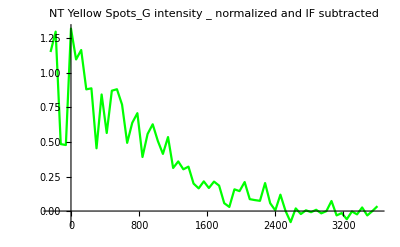

```mathematica
pfdata = ListLinePlot[ntGIntsYTime,PlotStyle->{Green},PlotLabel->"NT Yellow Spots_G intensity _ normalized and IF subtracted"]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
Clear@b
Clear@temp
Clear@ke
```

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[1.02329-0.000537371 t]

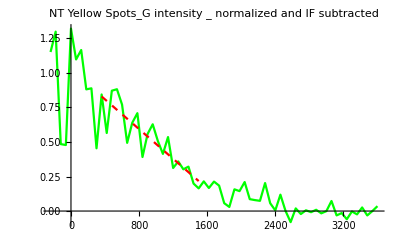

```mathematica
Show[pfdata, Plot[nlm[t],{t,(ntrangeA-5)*60,(ntrangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]]]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 0.922487 | 0.1201 | {0.670167,1.17481}
b | 1.02329 | 0.0694204 | {0.877438,1.16913}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.252321}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]]
```

0.922487±0.252321

#### TL: Fit and calculate elongation rate

```mathematica
fdata = tlRangedata;
```

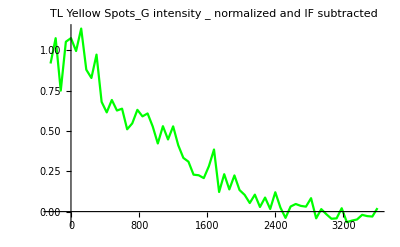

```mathematica
pfdata = ListLinePlot[tlGIntsYTime,PlotStyle->{Green},PlotLabel->"TL Yellow Spots_G intensity _ normalized and IF subtracted"]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[0.898377-0.000399178 t]

```mathematica
60*(tarangeA+5) ;; 60*(tarangeB + 5)
```

840;;1740

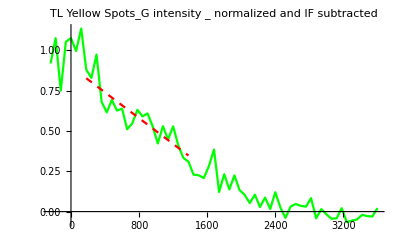

```mathematica
Show[pfdata, Plot[nlm[t],{t,(tlrangeA-5)*60,(tlrangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]]]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 0.685256 | 0.0802246 | {0.517344,0.853168}
b | 0.898377 | 0.0402119 | {0.814212,0.982541}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.167912}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]] (*AA per sec*)
```

0.685256±0.167912

#### TA: Fit and calculate elongation rate

```mathematica
fdata = taRangedata;
```

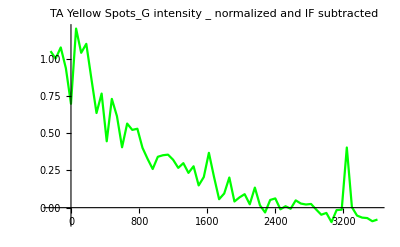

```mathematica
pfdata = ListLinePlot[taGIntsYTime,PlotStyle->{Green},PlotLabel->"TA Yellow Spots_G intensity _ normalized and IF subtracted"]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[0.865679-0.00051973 t]

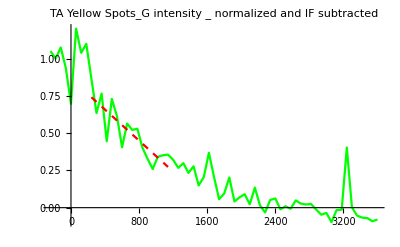

```mathematica
Show[pfdata, Plot[nlm[t],{t,(tarangeA-5)*60,(tarangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]]]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 0.892204 | 0.154565 | {0.560695,1.22371}
b | 0.865679 | 0.0669314 | {0.722125,1.00923}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.331508}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]] (*AA per sec*)
```

0.892204±0.331508

## White spots

#### Input:

```mathematica
myTimes = ntCounts[[1,2,1,All,1]]*60;
Length@myTimes
Length@ntCountsTot[[2,1,All,2]]
```

65

65

```mathematica
(*green intensity *) ntGIntsY0 = Table[Total@(Total/@ntWInts[[All,3,i]]),{i,1,Length@ntWInts[[1,2]],1}];
(*green intensity *) tlGIntsY0 = Table[Total@(Total/@tlWInts[[All,3,i]]),{i,1,Length@tlWInts[[1,2]],1}];
(*green intensity *) taGIntsY0 = Table[Total@(Total/@taWInts[[All,3,i]]),{i,1,Length@taWInts[[1,2]],1}];
```

#### FIRST, find the Immobile Fraction and subtract that out of the Y value...

#### NT: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = ntGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
immobileFraction = Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

0

0

0

«1 more identical outputs»

```mathematica
ntGIntsY00 = mySpots-immobileFraction ;
```

#### TL: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = tlGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
 Mean[mySpots[[45;;All]]]
immobileFraction =Mean[mySpots[[50;;All]]]
Mean[mySpots[[55;;All]]]
```

0.555433

0.49059

0.448169

0.416371

```mathematica
tlGIntsY00 = mySpots-immobileFraction ;
```

#### TA: calculating immobile fraction MANUAL INPUT: Set where you want the Immobile Fraction to be...

```mathematica
mySpots = taGIntsY0;
```

```mathematica
Mean[mySpots[[40;;All]]]
Mean[mySpots[[45;;All]]]
Mean[mySpots[[50;;All]]]
immobileFraction = Mean[mySpots[[54;;All]]]
```

1.9342

2.13654

2.54349

0.486139

```mathematica
taGIntsY00 = mySpots-immobileFraction ;
```

#### Normalizing Intensity...

```mathematica
tlGIntsY00
```

{3.67254,3.67916,3.99385,3.62754,4.07527,3.84149,3.55016,3.34904,3.26732,2.94513,2.62065,2.62459,2.61589,2.33276,1.83255,1.71588,1.73449,1.95249,1.46975,1.4263,1.09889,1.33619,1.02607,0.972528,1.03282,1.17187,1.0387,1.03535,1.03091,0.961008,0.971024,0.760661,0.775195,0.676636,0.579193,0.429495,0.353068,0.590619,0.536918,0.561133,0.289823,0.491057,0.252934,0.303097,0.144446,0.244545,0.214526,0.145015,0.142304,0.187171,0.13262,0.00974475,-0.0513593,0.0716003,-0.00874689,-0.151625,-0.117762,0.0247697,0.113531,0.0275536,-0.0776158,-0.0525587,-0.0919008,0.0794329,-0.0948547}

```mathematica
Mean[tlGIntsY00[[1;;7]]]
```

3.77715

```mathematica
(*normalized green intensity *) ntGIntsY = ntGIntsY00 /Mean[ntGIntsY00[[1;;7]]];
(*normalized green intensity *) tlGIntsY = tlGIntsY00 /Mean[tlGIntsY00[[1;;7]]];
(*normalized green intensity *)   taGIntsY =  taGIntsY00/Mean[taGIntsY00[[1;;7]]];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
(*normalized green intensity *) ntGIntsYTime = Transpose[{myTimes,ntGIntsY}] ;
(*normalized green intensity *) tlGIntsYTime =  Transpose[{myTimes,tlGIntsY}];
(*normalized green intensity *)   taGIntsYTime =   Transpose[{myTimes,taGIntsY}];
```

-Graphics-

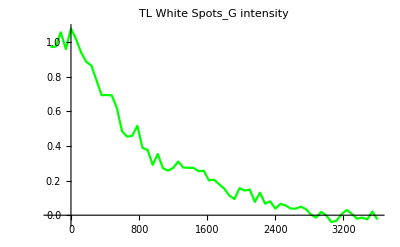

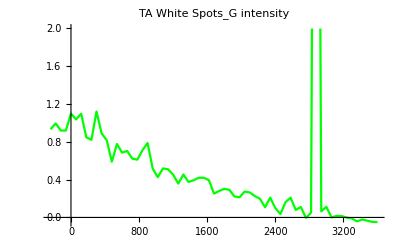

```mathematica
ListLinePlot[ntGIntsYTime,PlotStyle->{Green},PlotLabel->"NT White Spots_G intensity"]
ListLinePlot[tlGIntsYTime,PlotStyle->{Green},PlotLabel->"TL White Spots_G intensity"]
ListLinePlot[taGIntsYTime,PlotStyle->{Green},PlotLabel->"TA White Spots_G intensity"]
```

#### Define tag and protein lengths in AAs

```mathematica
l2 = (1010/3)//N   (*Length of smFLAG tag in AAs*)
l1 = (4645/3)//N   (*Length of KDM5B in AAs*)
```

336.667

1548.33

```mathematica
fraction = (l1/(l1+l2/2))   (*Once the fluorescence drops by this much, this is t0*)
```

0.901942

#### Select the data that falls within the linear range: l1/(l1+l2/2) --> linear part MANUAL INPUT: Set where you want the Linear Range to be...

```mathematica
(*Selecct the LINEAR range of hte graph above by looking at where it's linear and fittable and plugging the start and stop of this range into RangeA and RangeB *)
```

```mathematica
ListLinePlot[ntGIntsYTime/60,PlotStyle->{Green},PlotLabel->"NT WHITE Spots_G intensity _ normalized and IF subtracted"]
```

-Graphics-

```mathematica
ntrangeA = 14;
ntrangeB = 26;
ntRangedata =  ntGIntsYTime[[ntrangeA;; ntrangeB ]]
```

{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}}

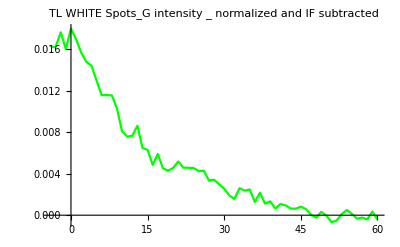

```mathematica
ListLinePlot[tlGIntsYTime/60,PlotStyle->{Green},PlotLabel->"TL WHITE Spots_G intensity _ normalized and IF subtracted"]
```

```mathematica
tlrangeA = 8;
tlrangeB = 20;
tlRangedata =  tlGIntsYTime[[tlrangeA;; tlrangeB ]]
```

{{180,0.88666},{240,0.865025},{300,0.779724},{360,0.693817},{420,0.694861},{480,0.692557},{540,0.617598},{600,0.485167},{660,0.45428},{720,0.459206},{780,0.516922},{840,0.389118},{900,0.377613}}

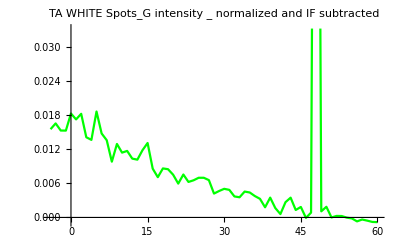

```mathematica
ListLinePlot[taGIntsYTime/60,PlotStyle->{Green},PlotLabel->"TA WHITE Spots_G intensity _ normalized and IF subtracted"]
```

```mathematica
tarangeA = 11;
tarangeB = 26;
taRangedata =  taGIntsYTime[[tarangeA ;; tarangeB ]]
```

{{360,0.888567},{420,0.817085},{480,0.589848},{540,0.777382},{600,0.685859},{660,0.703765},{720,0.622285},{780,0.611449},{840,0.711142},{900,0.787628},{960,0.516242},{1020,0.426081},{1080,0.518567},{1140,0.51029},{1200,0.451967},{1260,0.35803}}

#### Fit to the rate of elongation

### Fit to the rate of elongation

#### NT: Fit and calculate elongation rate

```mathematica
fdata = ntRangedata;
```

```mathematica
pfdata = ListLinePlot[ntGIntsYTime,PlotStyle->{Green},PlotLabel->"NT WHITE Spots_G intensity _ normalized and IF subtracted"]
```

-Graphics-

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t]

```mathematica
pntYnlm = Show[pfdata, Plot[nlm[t],{t,(ntrangeA)*60,(ntrangeB)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]]]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of FindFit::fitm will be suppressed during this calculation.

General::ivar: 840.015 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t][ParameterConfidenceIntervalTable]

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Differences::listrp: List or SparseArray or StructuredArray expected at position 1 in Differences[ParameterConfidenceIntervals].

Differences[ParameterConfidenceIntervals]/2

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]]
```

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Part::partd: Part specification NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t][BestFitParameters]⟦1,2⟧ is longer than depth of object.

FindFit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

Part::partd: Part specification NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t][BestFitParameters]⟦1,2⟧ is longer than depth of object.

NonlinearModelFit[{{540,Indeterminate},{600,Indeterminate},{660,Indeterminate},{720,Indeterminate},{780,Indeterminate},{840,Indeterminate},{900,Indeterminate},{960,Indeterminate},{1020,Indeterminate},{1080,Indeterminate},{1140,Indeterminate},{1200,Indeterminate},{1260,Indeterminate}},b-0.000582524 ke t,{{ke},{b}},t][BestFitParameters]⟦1,2⟧±1/2

#### TL: Fit and calculate elongation rate

```mathematica
fdata = tlRangedata;
```

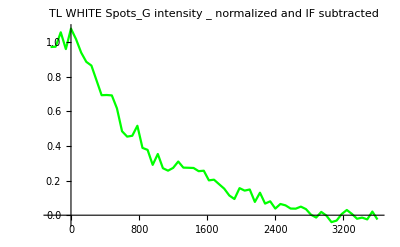

```mathematica
pfdata = ListLinePlot[tlGIntsYTime,PlotStyle->{Green},PlotLabel->"TL WHITE Spots_G intensity _ normalized and IF subtracted"]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[0.9982-0.000721374 t]

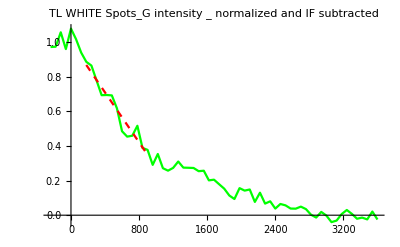

```mathematica
ptlWnlm =Show[pfdata, Plot[nlm[t],{t,(tlrangeA-5)*60,(tlrangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm]],PlotRange->{{All,2800},{0,1.3}}]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 1.23836 | 0.100159 | {1.01791,1.45881}
b | 0.9982 | 0.0341207 | {0.9231,1.0733}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.220449}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]] (*AA per sec*)
```

1.23836±0.220449

#### TA: Fit and calculate elongation rate

```mathematica
fdata = taRangedata;
```

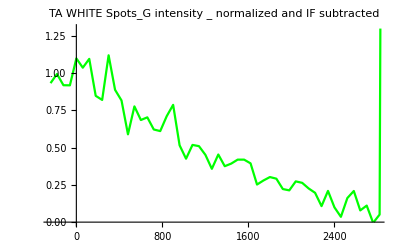

```mathematica
pfdata = ListLinePlot[taGIntsYTime,PlotStyle->{Green},PlotLabel->"TA WHITE Spots_G intensity _ normalized and IF subtracted",PlotRange->{{All,2800},{0,1.3}}]
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke},{b}},t]
```

FittedModel[0.982242-0.000442877 t]

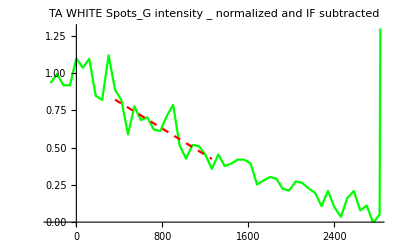

```mathematica
ptaWnlm =Show[pfdata, Plot[nlm[t],{t,(tarangeA-5)*60,(tarangeB-5)*60}, PlotStyle->{Red,Dashed},PlotLegends->Normal[nlm],PlotRange->{0,1.3}]]
```

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 0.760272 | 0.138643 | {0.462912,1.05763}
b | 0.982242 | 0.0691268 | {0.83398,1.1305}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
confinterval = Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{0.29736}

```mathematica
elongationrate =  PlusMinus[nlm["BestFitParameters"][[1,2]],confinterval[[1]]] (*AA per sec*)
```

0.760272±0.29736

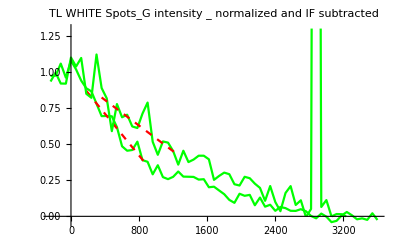

```mathematica
Show[ptlWnlm,ptaWnlm, PlotRange->{{All,2750},{0,1.3}}]
```

## DEVELOPMENT:

### ntWIntsTotRGB = Table[Table[Total@(Total /@ ntWInts[[All, j, i]]), {i, 1, Length@ntWInts[[1, 2]], 1}], {j, 2, Length@ntWInts[[2]], 1}]; tlWIntsTotRGB = Table[Table[Total@(Total /@ tlWInts[[All, j, i]]), {i, 1, Length@tlWInts[[1, 2]], 1}], {j, 2, Length@tlWInts[[2]], 1}]; taWIntsTotRGB = Table[Table[Total@(Total /@ taWInts[[All, j, i]]), {i, 1, Length@taWInts[[1, 2]], 1}], {j, 2, Length@taWInts[[2]], 1}];

### ListLinePlot[ntWIntsTotRGB, PlotStyle -> {Red, Green, Blue}, PlotLabel -> "NT White Spots"] ListLinePlot[tlWIntsTotRGB, PlotStyle -> {Red, Green, Blue}, PlotLabel -> "TL White Spots", PlotRange -> All] ListLinePlot[taWIntsTotRGB, PlotStyle -> {Red, Green, Blue}, PlotLabel -> "TA White Spots"]

## -Graphics-

## -Graphics-

## -Graphics-

## Filter out super bright spots.... DEVEL ONLY NOT USED

```mathematica
Mean/@taPIntsTotRGB
StandardDeviation/@taPIntsTotRGB
```

{2.74263,35285.9,4.22213}

{0.449464,246767.,0.877374}

```mathematica
Flatten@taPInts[[2,2;;All]]//ListPlot[#,PlotRange->All]&
```

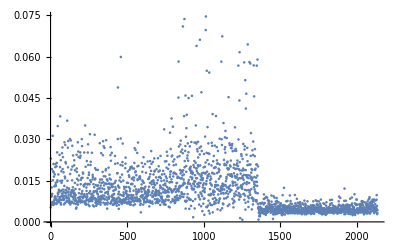

```mathematica
Flatten@taPInts[[2,2;;All]]//ListPlot[#,PlotRange->All]&
```

```mathematica
taPIntsTotRGB[[1]]
```

{2.47584,3.07414,2.86488,2.65799,2.62659,2.60375,2.60432,2.49616,2.39273,2.4301,2.62514,2.46654,1.54375,2.98487,2.5901,2.67558,2.83154,3.19738,3.04889,1.79608,3.07772,2.68259,2.81214,2.18564,3.14384,3.2118,2.66394,3.39831,2.77247,3.27428,2.87858,2.95246,3.14649,3.08243,2.82629,2.50264,2.21784,2.42245,2.89442,3.14418,1.75569,2.22796,2.17026,2.7947,2.30414,3.11704,2.57342,3.1438,2.44234,2.76412,2.49059,1.54537,3.02607,3.6355,3.44101,2.98863,3.41848,2.83269,2.76175,3.02623,2.83506,3.31131,3.42907,1.98778,2.9709}

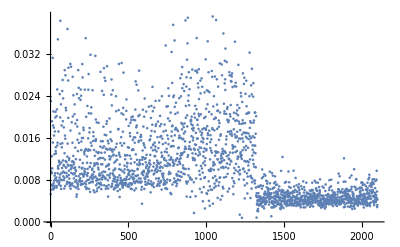

```mathematica
temp = Cases[Flatten@taPInts[[2]], x_/;x<.04];
ListPlot[temp,PlotRange->All]
```

## back to the code

```mathematica
ntPIntsTotRGB= Table[Table[Total@(Total/@ntPInts[[All,j,i]]),{i,1,Length@ntPInts[[1,2]],1}],{j,2,Length@ntPInts[[2]],1}];
tlPIntsTotRGB= Table[Table[Total@(Total/@tlPInts[[All,j,i]]),{i,1,Length@tlPInts[[1,2]],1}],{j,2,Length@tlPInts[[2]],1}];
taPIntsTotRGB= Table[Table[Total@(Total/@taPInts[[All,j,i]]),{i,1,Length@taPInts[[1,2]],1}],{j,2,Length@taPInts[[2]],1}];
```

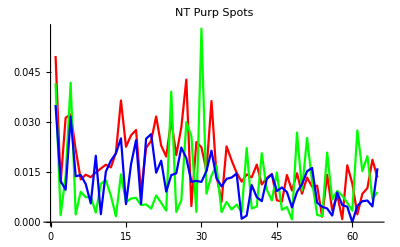

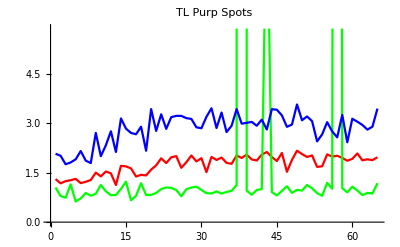

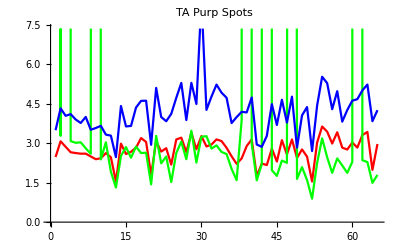

```mathematica
ListLinePlot[ntPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"NT Purp Spots"]
ListLinePlot[tlPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TL Purp Spots"]
ListLinePlot[taPIntsTotRGB,PlotStyle->{Red,Green,Blue},PlotLabel->"TA Purp Spots"]
```

```mathematica
Range[Length@taYIntsTotRGB]
```

{1,2,3}

## Fits:

### FIRST : take the immobile fraction adn average those spots. THIS is the Immobile fration. Subtract this # by all timepints NEW Length of the gene is JUST L1. ONLY USE the length of KDM5B, NOT plus smFLAG tag THEN, normalize my graphs to start at 1. THEN, Calculate (L1/(L1+L2/2))

### TA fits for green channel intensity over time

#### TA yellow spot fits

```mathematica
fdata = {{1, .7},{2, .45},{3, .2},{4,.01}}
```

{{1,0.7},{2,0.45},{3,0.2},{4,0.01}}

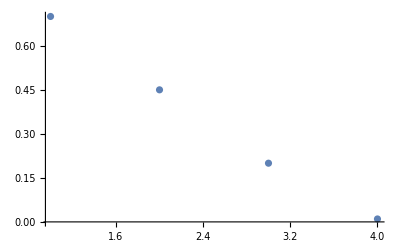

```mathematica
ListPlot[fdata]
```

```mathematica
l1 = 10;
l2 = 100;
```

```mathematica
(*l1*)
```

equation : y (ke, b) =  -ke/(L1 + L2/2)t +b

```mathematica
nlm=NonlinearModelFit[fdata ,-ke/(l1 + l2/2)t + b, {{ke,3},{b,2}},t]
```

FittedModel[0.92-0.232 t]

```mathematica
nlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
ke | 13.92 | 0.623538 | {11.2371,16.6029}
b | 0.92 | 0.0284605 | {0.797544,1.04246}

```mathematica
(*Confidence interval of the first element of the confidence, divide by 2 because it's + or - *)
Differences@nlm["ParameterConfidenceIntervals"][[1]]/2
```

{2.68287}

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[taYIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{5.79262-0.233167 x,5.57188-0.185193 x,5.37823-0.157267 x,5.20138-0.135775 x,5.03051-0.118205 x,4.91283-0.107987 x,4.77333-0.0975009 x,4.62915-0.0879299 x,4.48951-0.0795129 x,4.29081-0.068758 x,4.19658-0.0640402 x}

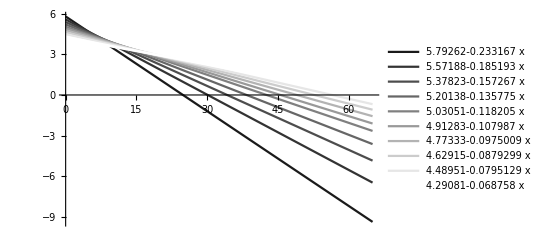

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→45.4945}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{24.8432,30.0869,34.198,38.3087,42.5577,45.4945,48.9568,52.6459,56.4626,62.4045,65.5303}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### TA White spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[taWIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{3.88556-0.125161 x,3.68528-0.086903 x,3.70961-0.0913791 x,3.6523-0.0848357 x,3.58215-0.0776633 x,3.50992-0.0715215 x,3.45484-0.0673555 x,3.38634-0.0628213 x,2.20961+0.00808293 x,2.55195-0.010663 x,2.78108-0.0221601 x}

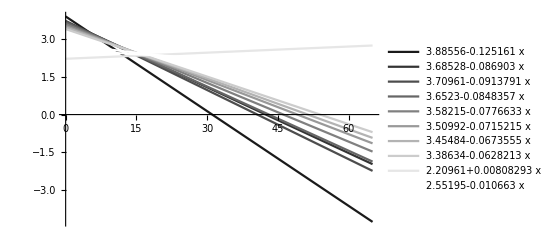

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

```mathematica
FindRoot[fits[[6]],{x,0}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→49.0751}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{31.0445,42.4068,40.5958,43.0515,46.1242,49.0751,51.2927,53.9044,-273.367,239.328,125.499}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### TA purple spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[taPIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{50.1529-3.02216 x,51.493-3.37974 x,45.9873-2.5512 x,40.4501-1.88278 x,35.9514-1.43025 x,-6.26353+2.10789 x,-39.4782+4.62208 x,-14.605+2.95637 x,7.57234+1.62007 x,22.388+0.80908 x,-9.14977+2.4851 x}

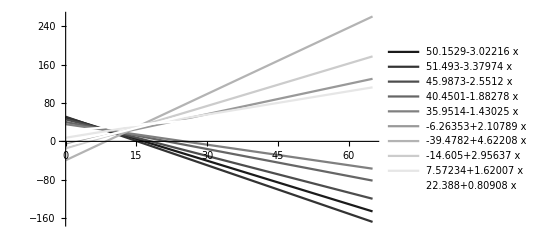

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{16.595,15.2358,18.0258,21.4843,25.1365,2.97147,8.54123,4.94017,-4.67409,-27.6709,3.68185}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

### TL fits for green channel intensity over time

#### TL yellow spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[tlYIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{3.6645-0.140717 x,3.45032-0.0995764 x,3.32379-0.0808464 x,3.33087-0.0814946 x,3.26202-0.0746307 x,3.22017-0.070997 x,3.15629-0.0662434 x,3.0849-0.0615204 x,2.99486-0.0560985 x,2.91706-0.0518532 x,2.82186-0.0471019 x}

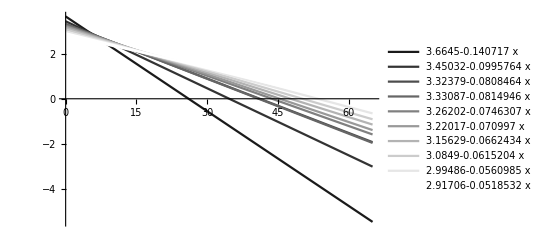

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→45.3565}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{26.0417,34.65,41.1124,40.8723,43.7088,45.3565,47.6469,50.1443,53.3857,56.2561,59.9096}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### TL White spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[tlWIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{4.66117-0.201336 x,4.53238-0.176423 x,4.39388-0.156016 x,4.13608-0.124865 x,3.95666-0.106739 x,3.80793-0.0940833 x,3.68066-0.0845049 x,3.55206-0.0759224 x,3.43914-0.0691394 x,3.32181-0.0627609 x,3.20528-0.0569349 x}

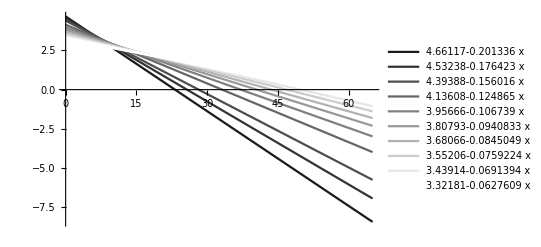

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→40.4741}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{23.1512,25.6903,28.163,33.1244,37.0686,40.4741,43.5556,46.7854,49.7422,52.9279,56.2973}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### TL purple spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[tlPIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{0.670645+0.0370692 x,0.795642+0.0101591 x,0.793366+0.0104097 x,0.809457+0.0082742 x,0.850046+0.00415539 x,-66.8208+5.86945 x,-33.5794+3.36145 x,-12.1254+1.92422 x,1.92363+1.07786 x,8.56933+0.717789 x,15.9538+0.347439 x}

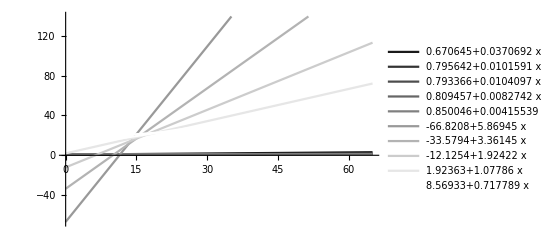

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{-18.0917,-78.3185,-76.214,-97.829,-204.565,11.3845,9.98954,6.30144,-1.78468,-11.9385,-45.9183}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

### NT fits for green channel intensity over time

#### NT yellow spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[ntYIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{1.70794-0.059297 x,1.67375-0.0530072 x,1.61917-0.0442865 x,1.61528-0.0437276 x,1.58922-0.0410968 x,1.53973-0.0369038 x,1.48924-0.0331015 x,1.44919-0.030414 x,1.40121-0.0275343 x,1.35138-0.0248065 x,1.29922-0.0221997 x}

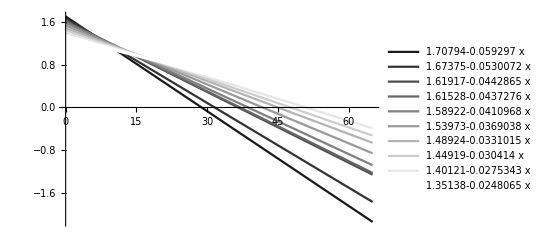

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→41.7229}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{28.8031,31.5758,36.5613,36.9395,38.6702,41.7229,44.9902,47.6488,50.8896,54.4769,58.5241}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### NT White spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[ntWIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

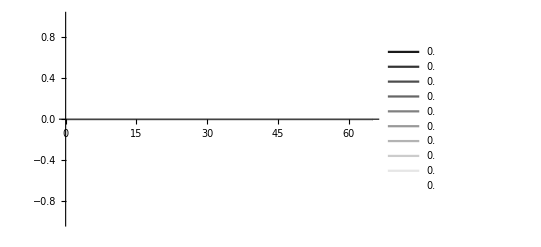

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

```mathematica
FindRoot[fits[[6]],{x,0}]
```

{x→0.}

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]//Cases[#,{x->x_}->x]&
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### NT purple spot fits

```mathematica
(*10 means start the fit at timept 10*)
fits = Table[Fit[ntPIntsTotRGB[[2]][[5;;i]],{1,x},x],{i, 15,65,5}]
```

{0.0058036+0.000295911 x,0.00764468-0.000074285 x,0.00541578+0.000250637 x,0.000859321+0.000777084 x,0.00454353+0.000408876 x,0.0069567+0.00019762 x,0.00763802+0.000145649 x,0.00847719+0.0000870209 x,0.00857304+0.0000822734 x,0.00960571+0.0000261275 x,0.00900533+0.0000575938 x}

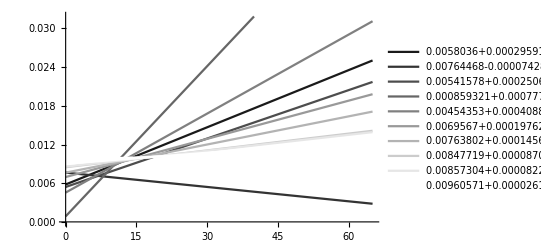

```mathematica
Plot[{fits},{x,0,65}, PlotStyle->Table[GrayLevel[i],{i,.1,Length@fits,.1}],PlotLegends->"Expressions"]
```

```mathematica
xints = Table[FindRoot[fits[[i]],{x,0}],{i,1,Length@fits,1}]
```

{{x→-19.6127},{x→102.91},{x→-21.608},{x→-1.10583},{x→-11.1123},{x→-35.2024},{x→-52.4414},{x→-97.4155},{x→-104.202},{x→-367.648},{x→-156.36}}

This graph shows the fits of regression in TA Yellow spots... I’m using 10 as the starting point so I don’t fit to the first 10 points (first 5 are pre-HT, next 5 are too early to see ribosome drop off bc they’re still translating the tag)

#### Conclusions

It looks like the elongation rates are SLOWER for the TA cells... Add more cells and see if this holds true!! 
I randomly picked the 6th fit to look at with each, I can redo this and look at different fits if Tim says that a different equation is better (I don’t really know how to discern between these...they all look good but get less and less sloped when you add more time points)

Also ask.... do I need to try nonlinear fits?

## Rate of Elongation:

```mathematica
lengthProtein= (4645 + 1010/2)
```

5150

```mathematica
lengthProteinAA = (4645 + 1010/2)/3//N
```

1716.67

The elongation time is the X-intercept MINUS the dead frames not used at the beginning of the movie (~8??) 
IN SECONDS

```mathematica
elongSec = (41.7-8)*60
```

2022.

```mathematica
lengthProteinAA/elongSec//N
```

0.848994

Amino Acids per second for NT...
SO, ~ half amino acid per second increase in time for TA white spots (slower TA translation rate)

```mathematica
Cases[test,{x->x_}->x]
```

{0.,0.}